Part::partd1: Depth of object SparseArray[Automatic,{16,16},0,{1,{{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32},{{1},{2},{1},{3},{3},{4},{4},{5},{5},{6},{6},{7},{7},{8},{8},{9},{9},{10},{10},{11},{11},{12},{12},{13},{13},{14},{14},{15},{15},{16},{2},{16}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}]⟦0,13⟧ is not sufficient for the given part specification.

Part::partd1: Depth of object {{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},«6»,{0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1}} is not sufficient for the given part specification.

13

12

14

Part::partd1: Depth of object SparseArray[Automatic,{16,16},0,{1,{{0,2,4,6,8,10,12,14,16,18,20,22,23,25,28,30,32},{{1},{2},{1},{3},{3},{4},{4},{5},{5},{6},{6},{7},{7},{8},{8},{9},{9},{10},{10},{11},{11},{12},{12},{13},{14},{14},{15},{13},{15},{16},{2},{16}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}]⟦0,12⟧ is not sufficient for the given part specification.

General::stop: Further output of Part::partd1 will be suppressed during this calculation.

12

11

7

16

15

1

( | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
2 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0
15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
16 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

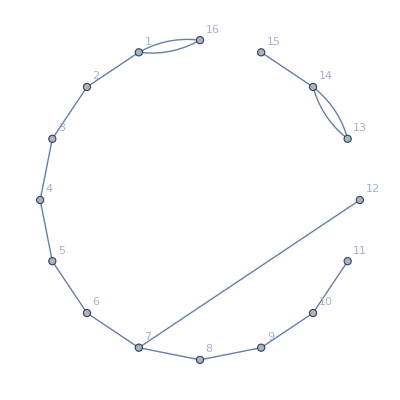

∞

```mathematica
ClearAll["Global`*"]
(*----------2 Rewireing Networks----------*)
(*----------Basic Setup----------*)
n=16;
r=3;


(*----------Distance Matrice between the nodes----------*)
m=IncidenceMatrix[CycleGraph[n]];
(*---m[[2,3]]=0; m[[7,3]]=1;---*)
(*----------Rewireing----------*)
(*-----m[[coloumn,row]]-----*)
miOld=0;
Do[
mjEdge=Random[Integer,{1,n}];
For[j=0,j<n,j++,
If[m[[j,mjEdge]]==1 && j≠mjEdge ,
miOld=j;
];
];
Label[againRandom];
miNew=Random[Integer,{1,n}];
If[miNew == mjEdge || miNew==miOld,Goto[againRandom],Goto[check]];
Label[check];
Print[mjEdge];
Print[miOld];
Print[miNew];
m[[miOld,mjEdge]]=0;
m[[miNew,mjEdge]]=1;
,r];

(*----------------------------*)


matrixLabel=Table[x,{x,n}];
MatrixForm[m, TableHeadings->{matrixLabel,matrixLabel}]

IncidenceGraph[m,VertexLabels->"Name",EdgeLabels->"Name"];
m=IncidenceGraph[m];
Table[Graph[m,GraphLayout->l,VertexLabels->Automatic],{l,{"CircularEmbedding"}}]

(*----------Average Path Length Calculation----------*)


(*----------Output----------*)
MeanGraphDistance[m]
```